# Vediamo sto EMG

```mathematica
emgNoMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/segnali_belli/EMGno.mat"];
numSamplesEmg = Dimensions[emgNoMatlab][[3]]
emgNoRaw =  Table[Transpose[emgNoMatlab[[1,1,x]]],{x,numSamplesEmg}];
```

30

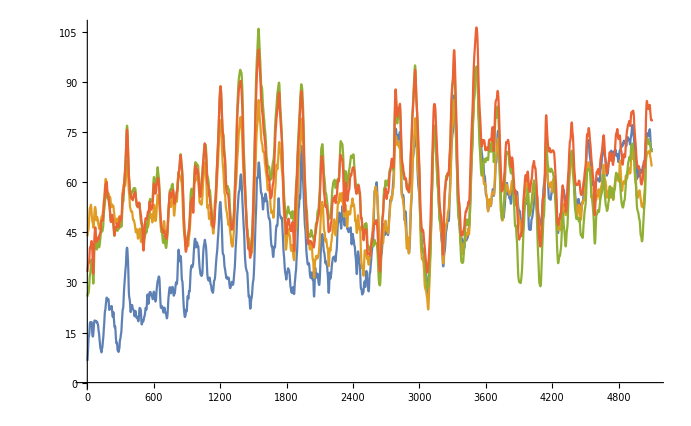

```mathematica
ListLinePlot@emgNoRaw[[1]]
```

```mathematica
Dimensions[emgNoRaw]
```

{30,4}

```mathematica
reducedEmgNo = Transpose[DimensionReduce[Transpose@#,2,Method->"PrincipalComponentsAnalysis"]]&/@emgNoRaw;
```

```mathematica
Dimensions[reducedEmgNo]
```

{30,2}

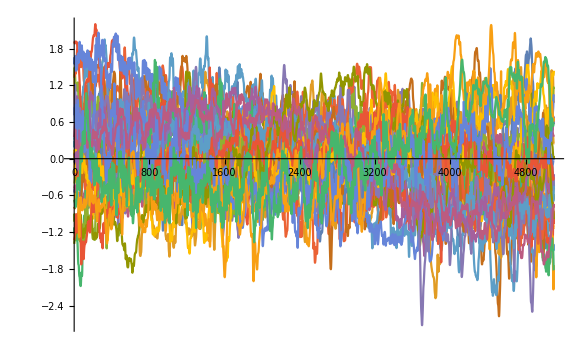

```mathematica
ListLinePlot[reducedEmgNo[[All,2]]]
```

```mathematica
check = FindClusters[reducedEmgNo[[All,1]],Method->"MeanShift"];
```

FindClusters::nosup: FindClusters does not support this type of data.